# Algunas aplicaciones de Wolfram Language

## Francisco Javier Rodríguez Arias Wolfram Research South America

## Motor de conocimiento

Wolfram|Alpha es el motor de conocimiento ofrecido por Wolfram Research y disponible vía diversas funciones desde el Wolfram Language.

### WolframAlpha

peru population

WolframAlphaQueryParseResults

30418591 people

peru population

peru population

WolframAlphaQueryResults

WolframAlpha::httperr: The request to URL http://www5a.wolframalpha.com/api/v2/recalc.jsp?appid=U2YPK6-9K5JY5YK6Y&id=MSPa79011f1ef856i3haf6ae000011362e0ia4c5a0002810311603729507317&uuid=None&mlicense=3725-4053-JWLTHE&machineid=6538-22451-34581&sig=cad2691425b3e8b2b25dc7830e04c7ce was not successful. The server returned the HTTP status code 500.

```mathematica
WolframAlpha["solve 1+x^2-2x=0"]
```

WolframAlphaQueryResults

### Entity framework

El entity framework permite al Wolfram Language acceder a la amplia base de conocimientos de Wolfram Alpha en forma sistemática.

#### Geografía

```mathematica
LinguisticAssistant
```

```mathematica
LinguisticAssistant[LinguisticAssistant]
```

30418591 people

```mathematica
LinguisticAssistant["Properties"]
```

```mathematica
GeoGraphics[Entity["Country","Peru"]]
```

-Graphics-

```mathematica
LinguisticAssistant
```

{Amazonas, Peru,Ancash, Peru,Apurímac, Peru,Arequipa, Peru,Ayacucho, Peru,Cajamarca, Peru,Callao, Peru,Cusco, Peru,Huancavelica, Peru,Huánuco, Peru,Ica, Peru,Junín, Peru,La Libertad, Peru,Lambayeque, Peru,Lima, Peru,Lima Provincias, Peru,Loreto, Peru,Madre de Dios, Peru,Moquegua, Peru,Pasco, Peru,Piura, Peru,Puno, Peru,San Martín, Peru,Tacna, Peru,Tumbes, Peru,Ucayali, Peru}

```mathematica
GeoGraphics[{EdgeForm[Black],Polygon/@LinguisticAssistant}]
```

-Graphics-

```mathematica
GeoRegionValuePlot[LinguisticAssistant->EntityProperty["Country","PopulationDensity"]]
```

-Graphics-

#### Química

```mathematica
Entity["Chemical","Water"]["MoleculePlot"]
```

-Graphics3D-

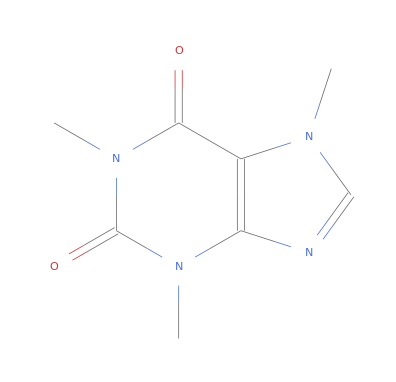

```mathematica
LinguisticAssistant[EntityProperty["Chemical","ColorStructureDiagram"]]
```

```mathematica
LinguisticAssistant["MoleculePlot"]
```

-Graphics3D-

#### Anatomía

```mathematica
AnatomyPlot3D[Entity["AnatomicalStructure","Arm"]]
```

```mathematica
AnatomyPlot3D[{Entity["AnatomicalStructure","SetOfCervicalVertebrae"]}]/.Annotation[x_,y_]:>{x,Black,Text[y["Name"],y["Entity"]["RegionCentroid"]+{45,0,0},{-1,0}]}
```

## Conocimiento lingüístico

### Transliterate

“Leer poema Chino”

```mathematica
Hyperlink["https://en.wikipedia.org/wiki/Lion-Eating_Poet_in_the_Stone_Den"]
```

```mathematica
string="施氏食獅史\n石室詩士施氏,\n嗜獅,誓食十獅.\n氏時時適市視獅.\n十時,適十獅適市.\n是時,適施氏適是市.\n氏視是十獅,恃矢勢,\n使是十獅逝世.\n氏拾是十獅屍,適石室.\n石室濕,氏使侍拭石室.\n石室拭,氏始試食十獅屍.\n食時,始識十獅屍,\n實十石獅屍.\n試釋是事.";
```

```mathematica
TextGrid[{{string,Transliterate[string,"Chinese"->"Latin"]}}]
```

施氏食獅史
石室詩士施氏,
嗜獅,誓食十獅.
氏時時適市視獅.
十時,適十獅適市.
是時,適施氏適是市.
氏視是十獅,恃矢勢,
使是十獅逝世.
氏拾是十獅屍,適石室.
石室濕,氏使侍拭石室.
石室拭,氏始試食十獅屍.
食時,始識十獅屍,
實十石獅屍.
試釋是事. | shī shì shí shī shǐ
shí shì shī shì shī shì,
shì shī, shì shí shí shī.
shì shí shí shì shì shì shī.
shí shí, shì shí shī shì shì.
shì shí, shì shī shì shì shì shì.
shì shì shì shí shī, shì shǐ shì,
shǐ shì shí shī shì shì.
shì shí shì shí shī shī, shì shí shì.
shí shì shī, shì shǐ shì shì shí shì.
shí shì shì, shì shǐ shì shí shí shī shī.
shí shí, shǐ shi shí shī shī,
shí shí shí shī shī.
shì shì shì shì.

### ¿Cuánto se parecen los idiomas?

```mathematica
IntegerName[10,"Russian"]
```

десять

```mathematica
Transliterate[%]
```

desat'

```mathematica
data=Association[#->IntegerName[Range[10],#]&/@{"Spanish","English","French","Portuguese","Italian","Romanian","German","Catalan","Polish","Danish","Swedish","Dutch","Russian","Serbian","Bosnian"}];
```

```mathematica
TextGrid[Join[Prepend[List/@(Style[#,Bold]&)/@Keys[data],{Null}],Prepend[data//Values,Range[10]],2],Frame->All]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
Spanish | uno | dos | tres | cuatro | cinco | seis | siete | ocho | nueve | diez
English | one | two | three | four | five | six | seven | eight | nine | ten
French | un | deux | trois | quatre | cinq | six | sept | huit | neuf | dix
Portuguese | um | dois | três | quatro | cinco | seis | sete | oito | nove | dez
Italian | uno | due | tre | quattro | cinque | sei | sette | otto | nove | dieci
Romanian | unu | doi | trei | patru | cinci | şase | şapte | opt | nouă | zece
German | eins | zwei | drei | vier | fünf | sechs | sieben | acht | neun | zehn
Catalan | u | dos | tres | quatre | cinc | sis | set | vuit | nou | deu
Polish | jeden | dwa | trzy | cztery | pięć | sześć | siedem | osiem | dziewięć | dziesięć
Danish | en | to | tre | fire | fem | seks | syv | otte | ni | ti
Swedish | ett | två | tre | fyra | fem | sex | sju | åtta | nio | tio
Dutch | een | twee | drie | vier | vijf | zes | zeven | acht | negen | tien
Russian | один | два | три | четыре | пять | шесть | семь | восемь | девять | десять
Serbian | један | два | три | четири | пет | шест | седам | осам | девет | десет
Bosnian | jedan | dva | tri | četiri | pet | šest | sedam | osam | devet | deset

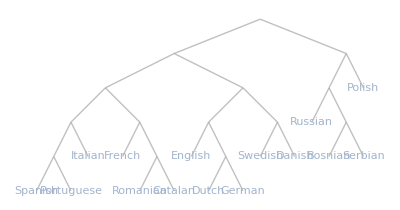

```mathematica
ClusteringTree[data,DistanceFunction->(Max[MapThread[EditDistance,Transliterate@{##}]]&),ImageSize->{Scaled[.8]}]
```

### Frecuencia

#### En un texto

```mathematica
texto=Import[FileNameJoin[{NotebookDirectory[],"textos","dqcap1.txt"}]];
```

```mathematica
StringTake[texto,500]
```

Que trata de la condición y ejercicio del famoso hidalgo don Quijote de la Mancha


En un lugar de la Mancha, de cuyo nombre no quiero acordarme, no ha mucho tiempo que vivía un hidalgo de los de lanza en astillero, adarga antigua, rocín flaco y galgo corredor. Una olla de algo más vaca que carnero, salpicón las más noches, duelos y quebrantos los sábados, lantejas los viernes, algún palomino de añadidura los domingos, consumían las tres partes de su hacienda. El resto della concluían sayo de ve

```mathematica
WordFrequency[texto,"don",IgnoreCase->True]
```

0.0031746

```mathematica
WordFrequency[texto,"hidalgo",IgnoreCase->True]
```

0.0021164

```mathematica
WordFrequency[texto,"de",IgnoreCase->True]
```

0.0645503

```mathematica
Take[WordCounts[texto],UpTo[50]]
```

<|de→122,y→103,que→88,a→43,el→39,su→35,en→35,la→34,se→30,con→26,le→23,los→21,no→19,del→19,por→17,lo→16,era→15,él→14,había→14,como→13,nombre→13,un→12,al→11,caballero→11,más→11,porque→9,todo→9,una→9,para→9,sin→8,cuando→8,así→8,las→8,bien→7,tan→7,vino→6,muy→6,razón→6,todos→6,sus→6,don→6,quien→5,celada→5,dio→5,Amadís→5,sido→5,ni→5,vuestra→5,estaba→5,o→5|>

#### Global e histórica

```mathematica
WordFrequencyData["de",Language->"Spanish"]
```

0.029847

```mathematica
vosotrosVSustedes=WordFrequencyData[{"vosotros","ustedes"},"TimeSeries",{1850,2008},Language->"Spanish"]
```

<|vosotros→TimeSeries[…],ustedes→TimeSeries[…]|>

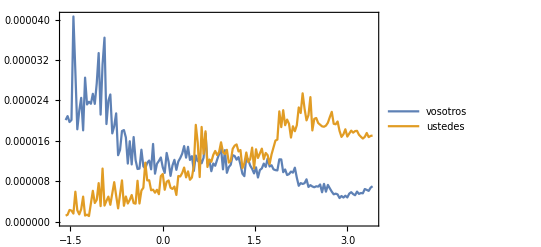

```mathematica
DateListPlot[vosotrosVSustedes]
```

```mathematica
nuevas=WordFrequencyData[{"ovni","televisor","internet","email"},"TimeSeries",{1900,2008},Language->"Spanish"]
```

<|ovni→TimeSeries[…],televisor→TimeSeries[…],internet→TimeSeries[…],email→TimeSeries[…]|>

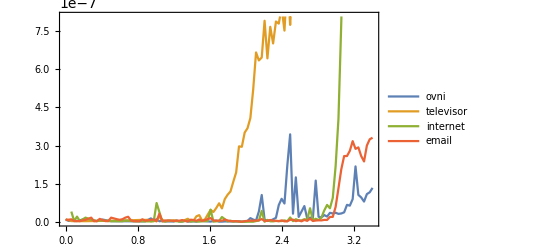

```mathematica
DateListPlot[nuevas]
```

## Procesamiento de imágenes

### Extrayendo partes

```mathematica
enElMisti=-Graphics-;
```

```mathematica
map=ImageAdjust@ImageSaliencyFilter[enElMisti,Method->"ImageSignature"]
```

-Graphics-

```mathematica
mask=DeleteSmallComponents@Dilation[Binarize[map,1/3],2]
```

-Graphics-

```mathematica
HighlightImage[enElMisti,mask,"Lighten"]
```

-Graphics-

```mathematica
Show[ImageTrim[enElMisti,ComponentMeasurements[mask,"BoundingBox"][[1,2]],20],ImageSize->500]
```

-Graphics-

```mathematica
Inpaint[enElMisti,mask]
```

-Graphics-

### Image focus

```mathematica
list = {-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-};
```

```mathematica
clean=Inpaint[#,Dilation[Binarize[#,{0,.1}],1]]&/@list;
ListAnimate[clean]
```

```mathematica
ImageFocusCombine[clean]
```

-Graphics-

### Alineando imágenes panorámicas

```mathematica
{i1,i2}=Import[FileNameJoin[{NotebookDirectory[],"imagenes",#}]]&/@{"imagen1.jpg","imagen2.jpg"};
```

```mathematica
Thumbnail/@{i1,i2}
```

{-Graphics-,-Graphics-}

```mathematica
{e,tr}=FindGeometricTransform[i1,i2]
```

{0.513671,TransformationFunction[(0.764251 | -0.00758637 | 2262.07
-0.0706949 | 0.945581 | -72.0772
-0.000060288 | 2.33541×10^-6 | 1.)]}

```mathematica
{w,h}=ImageDimensions[i2]
```

{3968,2976}

```mathematica
i2transform=ImagePerspectiveTransformation[i2,tr,DataRange->Full,PlotRange->{{0,First@tr[{w,0}]},{0,h}},Background->Transparent,Masking->All];
```

```mathematica
ImageCompose[i2transform,{i1,.99},{0,0},{0,0}]
```

```mathematica
With[{i2tr=ImageResize[i2transform,Scaled[.025]],i1r=ImageResize[i1,Scaled[.025]]},Manipulate[ControlActive[Image[ImageCompose[i2tr,{i1r,α},{0,0},{0,0}],ImageSize->1000],ImageResize[ImageCompose[i2transform,{i1,α},{0,0},{0,0}],1000]],{α,0,1}]]
```

### Buscando caras

```mathematica
conSW=-Graphics-;
```

#### Funciones

```mathematica
hightlightFaces[i_Image,size_]:=HighlightImage[i,Graphics[{White,Rectangle@@@FindFaces[i,size]},Background->Black],Method->"Boundary"]
```

```mathematica
extractFaces[i_Image,size_,margen_:10]:=ImageTrim[i,#,margen]&/@FindFaces[i,size]
```

#### Aplicación

```mathematica
hightlightFaces[conSW,{50,200}]
```

-Graphics-

```mathematica
extractFaces[conSW,{50,200},30]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Identify, Recognize, Classify!

Wolfram Language provee diversas funciones para la identificación y clasificación de información. Algunas de estas funciones son LanguageIdentify, ImageIdentify, Classify, NetTrain, etc.

### Identificando idiomas

```mathematica
LanguageIdentify["esta frase"]
```

Spanish

```mathematica
LanguageIdentify["привет"]
```

Russian

### Identificando imágenes

```mathematica
actriz=-Graphics-;
```

```mathematica
ImageIdentify[actriz]
```

person

```mathematica
plaza=-Graphics-;
```

```mathematica
ImageIdentify[plaza]
```

church

### BarcodeRecognize

```mathematica
BarcodeRecognize[-Graphics-]
```

### TextRecognize

```mathematica
TextRecognize[-Graphics-,Language->{"German","Russian","Spanish"}]
```

Drinnen saßen stehend Leute
Schweigend ins Gespräch verlief!

русский текст написанный на кирилице

El hardware inalámbrico no autorizado se puede
introducir fácilmente.

```mathematica
TextRecognize[-Graphics-]
```

… I
I .. | 1
“*: X '
»
E
J J ¡
_ __.ba

PROHIBITED
STREET VENDING

## Classify! (1)

La función Classify permite usar motores de clasificación incluidos en el lenguage así como construir clasificadores basados en nuestra propia data.

### Motores incluidos

Entre los motores incluidos en Classify, podemos encontrar el de “NotablePerson”:

#### “NotablePeson”

```mathematica
yo=-Graphics-;
```

```mathematica
Classify["NotablePerson",yo]
```

Carl Sagan

```mathematica
Classify["NotablePerson",yo,"TopProbabilities"]
```

{Carl Sagan→0.25043,Barack Obama→0.158414,Shahrukh Khan→0.142846,Ivan Ochoa→0.0890739,Malala Yousafzai→0.0584448,Freddie Mercury→0.025486}

```mathematica
Classify["NotablePerson",actriz]
```

```mathematica
Grid[{#,Classify["NotablePerson",#]}&/@extractFaces[conSW,{50,200},20],Frame->All]
```

-Graphics- | Ivan Ochoa
-Graphics- | Stevie Nicks
-Graphics- | Stephen Wolfram
-Graphics- | Val Kilmer

```mathematica
Grid[{#,Classify["NotablePerson",#,"TopProbabilities"]}&/@extractFaces[conSW,{50,200},20],Frame->All]
```

-Graphics- | {Ivan Ochoa→0.33009,Justin Bieber→0.0851334,Lee Min-ho→0.0621404,Malala Yousafzai→0.0427221,Russell Brand→0.0404611,Steven Tyler→0.0379572,Dave Grohl→0.0372015}
-Graphics- | {Stevie Nicks→0.783291}
-Graphics- | {Stephen Wolfram→0.99526}
-Graphics- | {Val Kilmer→0.143986,Tim Tebow→0.10252,Ryan Dunn→0.0869758,Wayne Rooney→0.0680144,Corey Haim→0.0437939,Callum Nicoll→0.0411385,Janis Joplin→0.0356745,Randy Orton→0.0246623,Will Sowles→0.0246037,Chris Jericho→0.0244855,Ivan Ochoa→0.0235655,Anderson da Silva→0.0186245,Mikhail Gorbachev→0.0177567}

#### Facial features

```mathematica
AssociationMap[Classify[#,yo]&,{"FacialAge","FacialExpression","FacialGender"}]
```

<|FacialAge→49,FacialExpression→happiness,FacialGender→Male|>

```mathematica
Classify["FacialAge",yo,"TopProbabilities"]
```

{49→0.0543468,47→0.0507149,46→0.0461193,50→0.0439065,48→0.0432224,51→0.0412066,41→0.0402358,43→0.0391414,54→0.0384397,52→0.0367741,42→0.0365353,45→0.0358457,40→0.0344096,53→0.0340528,44→0.0291643,55→0.0281869,56→0.0276776,36→0.0257839,38→0.0237204,39→0.0208705,58→0.0197435,35→0.0192336,57→0.0175017,34→0.0171616,37→0.0168804,33→0.0148876,32→0.0134734,60→0.0116124,59→0.0115004,61→0.00917162,29→0.00836085,30→0.00819386,31→0.00817327,28→0.00797021,62→0.00632162,27→0.00602062}

```mathematica
AssociationMap[Classify[#,actriz]&,{"FacialAge","FacialExpression","FacialGender"}]
```

<|FacialAge→24,FacialExpression→neutral,FacialGender→Female|>

```mathematica
Grid[{#,Classify["FacialAge",#]}&/@extractFaces[conSW,{50,200},20],Frame->All]
```

-Graphics- | 23
-Graphics- | 62
-Graphics- | 52
-Graphics- | 36

```mathematica
Grid[{#,Classify["FacialExpression",#,"TopProbabilities"]}&/@extractFaces[conSW,{50,200},20],Frame->All]
```

-Graphics- | {happiness→0.928946}
-Graphics- | {happiness→0.733498,neutral→0.226513}
-Graphics- | {neutral→0.518935,happiness→0.388742}
-Graphics- | {neutral→0.513805,happiness→0.335253,sadness→0.0713417,anger→0.064727}

```mathematica
Grid[{#,Classify["FacialGender",#]}&/@extractFaces[conSW,{50,200},20],Frame->All]
```

-Graphics- | Male
-Graphics- | Female
-Graphics- | Male
-Graphics- | Male

#### “NameGender”

```mathematica
Classify["NameGender","Francisco"]
```

Male

```mathematica
Classify["NameGender","Eustaquio"]
```

Male

```mathematica
Classify["NameGender","Kelly"]
```

Female

```mathematica
Classify["NameGender","Kelly","Probabilities"]
```

<|Female→0.859313,Male→0.140687|>

#### “ProgrammingLanguage”

```mathematica
Classify["ProgrammingLanguage","Classify[\"Language\", \"hola\"]"]
```

Wolfram Language

```mathematica
Classify["ProgrammingLanguage","int main() {int i; i = 0; return i;}"]
```

C

```mathematica
Classify["ProgrammingLanguage","def x:
	return 1"]
```

Python

#### “CountryFlag”

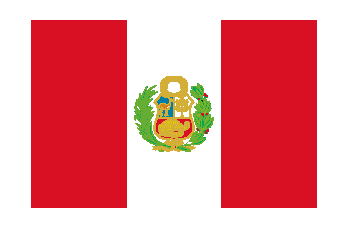
```mathematica
Classify["CountryFlag",-Graphics-]
```

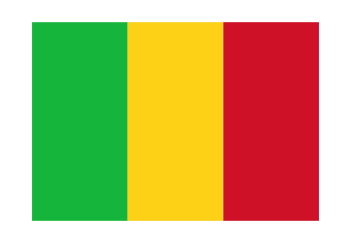
```mathematica
Classify["CountryFlag",-Graphics-]
```

```mathematica
Classify["CountryFlag",-Graphics-]
```

¿País aleatorio?

```mathematica
randomCountryFlag=CountryData[randomCountry=RandomChoice[CountryData[]],"FlagImage"]
```

```mathematica
classifyCountryResult=Classify["CountryFlag",randomCountryFlag]
```

```mathematica
randomCountry==classifyCountryResult
```

#### Sentimientos y otros

```mathematica
Classify["Profanity","all right!"]
```

```mathematica
Classify["Profanity","what the hell?"]
```

```mathematica
Classify["Sentiment","I'm feeling happy"]
```

```mathematica
Classify["FacebookTopic","The president should say something."]
```

## Classify! (2)

### Creando mi propio clasificador: ¿Qué personaje eres del chavo del ocho?

#### Importando imágenes

```mathematica
imagenesPorPersonaje=AssociationMap[With[{perdir=FileNameJoin[{NotebookDirectory[],"imagenes",URLEncode[#]}]},DeleteDuplicates@Select[Flatten[(Import/@FileNames["*",perdir])],ImageQ]]&,{"Roberto Gómez Bolaños","Carlos Villagrán","María Antonieta de las Nieves","Ramón Valdés","Florinda Meza","Rubén Aguirre","Édgar Vivar","Angelines Fernández"}];
```

```mathematica
RandomSample[#,3]&/@imagenesPorPersonaje
```

-Graphics-

```mathematica
Length/@imagenesPorPersonaje
```

<|Roberto Gómez Bolaños→71,Carlos Villagrán→60,María Antonieta de las Nieves→53,Ramón Valdés→39,Florinda Meza→42,Rubén Aguirre→57,Édgar Vivar→18,Angelines Fernández→139|>

#### Creando clasificador

```mathematica
clasificador=Classify[imagenesPorPersonaje]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[clasificador]
```

Classifier information
Input type | Image
Number of classes | 8
Method | LogisticRegression
Accuracy | 74. % ± 4.5 %
Loss | 0.986 ± 0.16
Evaluation time | 51.7 µs/example
Classifier memory | 1.52 MB
Training examples used | 479 examples
Training time | 58.6 s
 |

#### Usando clasificador

```mathematica
clasificador@actriz
```

Florinda Meza

```mathematica
clasificador@yo
```

Florinda Meza

```mathematica
Column[#->clasificador[#]&/@extractFaces[conSW,{50,200},20]]
```

-Graphics-→María Antonieta de las Nieves
-Graphics-→María Antonieta de las Nieves
-Graphics-→Carlos Villagrán
-Graphics-→Carlos Villagrán

#### Mejorando clasificador

```mathematica
imagenesPorPersonaje1Face=Pick[#,Length/@FindFaces/@#,1]&/@imagenesPorPersonaje;
```

```mathematica
Length/@imagenesPorPersonaje1Face
```

<|Roberto Gómez Bolaños→42,Carlos Villagrán→43,María Antonieta de las Nieves→33,Ramón Valdés→32,Florinda Meza→29,Rubén Aguirre→36,Édgar Vivar→14,Angelines Fernández→128|>

```mathematica
RandomSample[#,3]&/@imagenesPorPersonaje1Face
```

```mathematica
clasificadorMejorado=Classify[imagenesPorPersonaje1Face]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[clasificadorMejorado]
```

Classifier information
Input type | Image
Number of classes | 8
Method | LogisticRegression
Accuracy | 76.1 % ± 5.1 %
Loss | 1.06 ± 0.09
Evaluation time | 64.1 µs/example
Classifier memory | 1.25 MB
Training examples used | 357 examples
Training time | 43.2 s
 |

```mathematica
clasificadorMejorado@actriz
```

```mathematica
clasificadorMejorado@yo
```

Florinda Meza

```mathematica
Column[#->clasificadorMejorado[#]&/@extractFaces[conSW,{50,200},20]]
```